# ListDensityPlot de 1/100∫_0^100 𝔼[Tr[𝒟^2(t)] ]dt

```mathematica
SetDirectory[NotebookDirectory[]];
```

## XXZ L=7,d=4,J_z=1,ω=0, barriendo ε y J_xy de 0 a 2 (paso = 0.1)

```mathematica
(* Datos del promedio temporal del valor esperado de Haar de la pureza de Choi *)
{#[[1]],choiPurity=#[[2;;]];}&[Import["data/temporal_haar_avg_choi_purity/xxz_w_defect_L_7_Jz_1_d_4_omega_0.csv"]]
```

{{\varepsilon,J_{xy},promedio temporal de 0 a 100 del valor esperado de Haar de la pureza de Choi},Null}

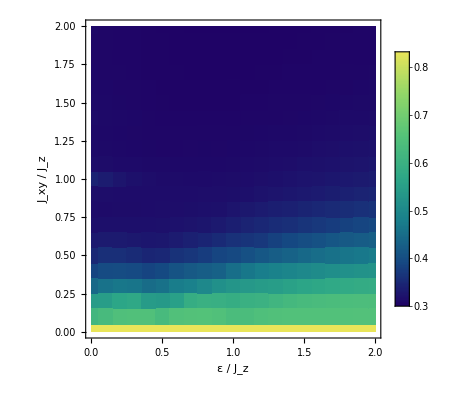

```mathematica
fontSize=22;

fig=ListDensityPlot[choiPurity,
ColorFunction->"BlueGreenYellow",
InterpolationOrder->0,
PlotLegends->Placed[BarLegend[Automatic,LabelStyle->Directive[FontFamily->"Arial",FontSize->fontSize,Black]],Automatic],
Frame->True,
FrameStyle->Directive[FontFamily->"Arial",FontSize->fontSize,Black],
FrameLabel->{"ε / J_z","J_xy / J_z"}
]
```

```mathematica
Export["tmp/temporal_avg_haar_avg_choi_purity_xxz_L_7_Jz_1_omega_0_d_4.png",fig,"PNG"]
```

tmp/temporal_avg_haar_avg_choi_purity_xxz_L_7_Jz_1_omega_0_d_4.png

## XXZ L=7,d=3,J_z=1,ω=0, barriendo ε y J_xy de 0 a 2 (paso = 0.1)

```mathematica
(* Datos del promedio temporal del valor esperado de Haar de la pureza de Choi *)
{#[[1]],choiPurity=#[[2;;]];}&[Import["data/temporal_haar_avg_choi_purity/xxz_w_defect_L_7_Jz_1._d_3_omega_0..csv"]]
```

{{\varepsilon,J_{xy},promedio temporal de 0 a 100 del valor esperado de Haar de la pureza de Choi},Null}

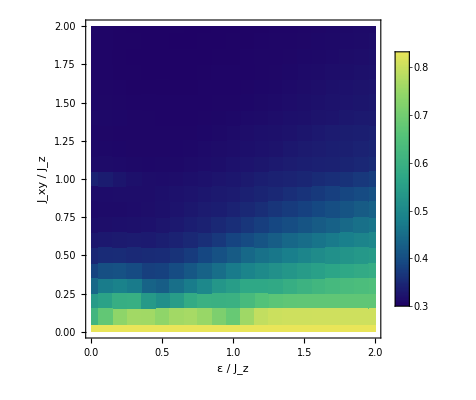

```mathematica
fontSize=22;

fig=ListDensityPlot[choiPurity,
ColorFunction->"BlueGreenYellow",
InterpolationOrder->0,
PlotLegends->Placed[BarLegend[Automatic,LabelStyle->Directive[FontFamily->"Arial",FontSize->fontSize,Black]],Automatic],
Frame->True,
FrameStyle->Directive[FontFamily->"Arial",FontSize->fontSize,Black],
FrameLabel->{"ε / J_z","J_xy / J_z"}
]
```

```mathematica
Export["tmp/temporal_avg_haar_avg_choi_purity_xxz_L_7_Jz_1_omega_0_d_3.png",fig,"PNG"]
```

tmp/temporal_avg_haar_avg_choi_purity_xxz_L_7_Jz_1_omega_0_d_3.png